```mathematica
σ = 1; a= 1;ϵ=5 10^-4;Ω = 2; α = 1/(a σ)^2; λ = 10^-2;
```

```mathematica
DD[x_, y_,L_, Ω_]:= a/(32 π^2)((((a L)/2 - ⅇ^(-(x a)/2)Sinh[(y a)/2])((a L)/2 + ⅇ^((x a)/2)Sinh[(y a)/2]) -I ϵ)^-1 
                                                         +   (((a L)/2 + ⅇ^(-(x a)/2)Sinh[(y a)/2])((a L)/2 - ⅇ^((x a)/2)Sinh[(y a)/2]) -I ϵ)^-1);
```

```mathematica
X[Ω_,L_]:=NIntegrate[ⅇ^(-(x^2 + y^2)/(4 σ^2) - ⅈ x Ω) DD[x, y,L, Ω], {y,0,5σ},{x,-5 σ, 5σ},MinRecursion->4];
(*{x,-5 σ,-5  σ+I ϵ,5 σ+I ϵ, 5σ}*)
```

```mathematica
test1=ParallelTable[{L,X[Ω,L]},{L,1/10,1,1/10}];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00219697+0.0212265 ⅈ and 0.0604185 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00170925+0.078839 ⅈ and 0.000016063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00136449+0.0401727 ⅈ and 0.00627768 for the integral and error estimates.

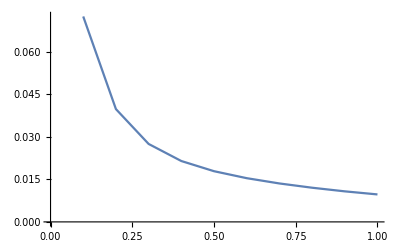

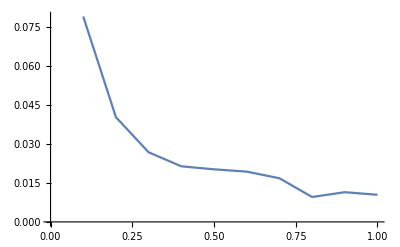

```mathematica
ListPlot[Abs[test1],Joined->True]
```

```mathematica
P[Ω_, L_]:=(λ^2 a σ)/(4 π^(3/2))      ∫_(10^-2)^(4α) Cos[(2s Ω)/a] ⅇ^(−s^2 α) (Sinh[s]^2 - s^2)/(Sinh[s]^2 s^2) ⅆs    +    λ^2/(4π)(ⅇ^(-Ω^2 σ^2) -√π Ω σ Erfc[Ω σ] )
```

```mathematica
Conc[Ω_, L_]:=2Max[0, Abs[X[Ω,L]] - P[Ω, L]]
```

```mathematica
Cs = ParallelTable[{L,Conc[Ω, L]}, {L,0.01,1.4, 0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0828825,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.0106849+1.68898×10^-11 ⅈ and 3.09309×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.10748,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.0106133+1.56393×10^-11 ⅈ and 1.15963×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0664769,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.00951077-2.00683×10^-11 ⅈ and 2.67325×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0172377,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.0023786+2.02606×10^-9 ⅈ and 1.62773×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0500677,5.+0.00016775221478718565015736788135371153568504070053588053377564755735 ⅈ}. NIntegrate obtained 0.00719723-4.87891×10^-19 ⅈ and 4.2758×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0992821,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.0108277-2.67831×10^-12 ⅈ and 7.15014×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.000820846,5.+0.00016775221478718565015736788135371153568504070053588053377564755735 ⅈ}. NIntegrate obtained 0.00171662+2.38454×10^-8 ⅈ and 0.0000215565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0336538,5.+0.00016775221478718565015736788135371153568504070053588053377564755735 ⅈ}. NIntegrate obtained 0.00432796-4.29842×10^-10 ⅈ and 6.53554×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0254462,5.+0.00016775221478718565015736788135371153568504070053588053377564755735 ⅈ}. NIntegrate obtained 0.00314474+8.73857×10^-10 ⅈ and 1.67326×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.00902955,5.+0.00016775221478718565015736788135371153568504070053588053377564755735 ⅈ}. NIntegrate obtained 0.00198421+1.21939×10^-9 ⅈ and 5.6745×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0910829,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.0108662-2.63324×10^-12 ⅈ and 8.4296×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0582729,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.00848303+1.39927×10^-11 ⅈ and 2.07403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {y,x} = {0.0746804,5.+6.7104206529942183006072742709690430949430446322721224484991909229×10^-6 ⅈ}. NIntegrate obtained 0.010243-6.15549×10^-12 ⅈ and 9.24738×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {y,x} = {0.0418602,-5.+6.7104206530063613649391119206299265663127879794400911984991909229×10^-6 ⅈ}. NIntegrate obtained 0.00575388+4.89907×10^-12 ⅈ and 1.85067×10^-7 for the integral and error estimates.

$Aborted

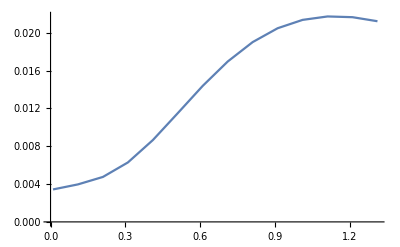

```mathematica
ListPlot[Cs, Joined -> True]
```